# Differential Equations for High School Students

Kyungwon Chun
ruddyscent@gmail.com
BioBrain Inc.

```mathematica
DateString[]
$Version
<<SymbolicComputing`
$SCVersion
```

Mon 29 Apr 2019 14:13:53

11.3.0 for Mac OS X x86 (64-bit) (March 7, 2018)

5.0.4 (August 5, 2018)

## Reference

W. E. Boyce and R. C. DiPrima, Elementary Differential Equations and Boundary Value Problems, 10th ed. Wiley, 2012.

-Graphics-
William E. Boyce

## 0 MathSymbolica

## Overview

Mathematica add-on package that facilitates symbolic computation with mathematical expressions

Over 850 functions and own programming language

Display and interpretation of various mathematical expressions like derivatives, integrals, sums, vector operators, brakets, etc. using the traditional notation

## Author

-Graphics-

Ph.D Youngjoo Chung
Professor
School of Information and Communications
Gwangju Institute of Science and Technology (GIST), South Korea
E-mail: ychung@gist.ac.kr

## Keywords

Notation,
Manipulation and
Evaluation
of Mathematical Expressions

## Motivation

To design and implement a symbolic computing system based on Mathematica that can manipulate various mathematical expressions using traditional notation and deferred on-demand evaluation

## Objective

To replace hand-written calculation with symbolic computation and software-based automation

## Features

Allows traditional notation for various mathematical expressions

Algebraic manipulation of formulas using symbolic computation

Seamless integration with the computing environment of Mathematica

Powerful platform for streamlined manipulation of mathematical expressions

## Advantages

Close emulation of hand-written calculation

Allows focusing on concepts and principles rather than tedious, boring, time-consuming and error-prone hand-written calculation

Good readability, enhanced speed and accuracy, and minimization of human errors during calculation

Expressions that closely resemble the traditional mathematical style, e.g., subscripts, derivatives and vector operators

## Brief History

2002. 04: Development started as MiscAlgebra Package (MP)
2007. 11: Presented at the First Korean Mathematica Users Conference
2011. 08: Renamed to Symbolic Computing (SC) Package
2011. 10: Presented at Wolfram Technology Conference 2011
2012. 02: Version 1.0 beta release after the lecture at Mathematics Dept of Korea University
2012. 04: Version 2.0 beta
2014. 12: Version 3.0 beta
2015. 10: Version 3.1 beta
2016. 06: Version 4.0 beta
2017. 12: Version 4.1 (commercial release)
2018. 06: Version 5.0 release

## Installation

```mathematica
ToExpression[URLFetch["https://symbcomp.gist.ac.kr/downloads/InstallSymbComp.m"]]
```

## 1 Introduction

## Historical Remarks

Isaac Newton (1642-1727)
-Graphics-

1687: published Philosophiae Naturalis Principia Mathematica
-Graphics-

1705: knighted

1727: burried in Westminster Abbey
-Graphics-

Gottfried Wilhelm Leibniz (1646-1716)
-Graphics-

1684: published the fundamental results of calculus

1691: invented separation of variables

1694: solved the first order linear equations

## Determinism

-Graphics-+-Graphics-=-Graphics-

## 1.1 Some Basic Mathematical Model; Direction Fields

### Example 1: A Falling Object

-Graphics-

The physical law that governs the motin of objects in Newton’s second law expressed by the equation;

```mathematica
F==m a(*eq1.1*)
SCMAF[%,RA,{At[2],a==ⅆv/ⅆt}]
```

F==a m

F==m ⅆv/ⅆt

where m is the mass of th eobject, v is its velocity,  a is its acceleration, and F is the net force exerted on the object, while t denotes time.

```mathematica
F==m g-γ v(*eq1.3*)
SCMAF[%,RA,{At[1],F==m ⅆv/ⅆt},
SCDivEq,{All,m}]
```

F==g m-v γ

m ⅆv/ⅆt==g m-v γ

ⅆv/ⅆt==g-(v γ)/m

where g is the acceleration due to gravity near the earth’s surface, and γ is a drag coefficient.

### Example 2: A Falling Object (continued)

-Graphics-

```mathematica
ⅆv/ⅆt==g-(v γ)/m(*eq1.4*)
SCMAF[%,RA,{At[2],{γ==2,m==10,g==9.8}}]
(*eq1.5*)
```

ⅆv/ⅆt==g-(v γ)/m

ⅆv/ⅆt==9.8-v/5

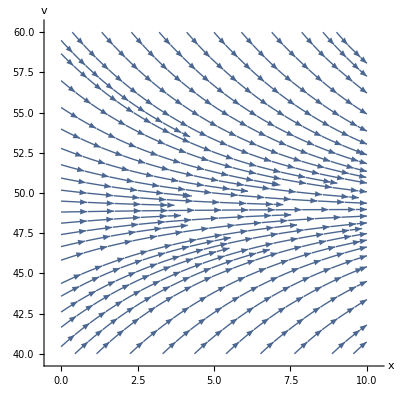

```mathematica
StreamPlot[{1,9.8-v/5},{t,0,10},{v,40,60},Frame->False,Axes->True,AxesLabel->{x,v},AspectRatio->1](*fig1.1.2*)
```

When ⅆv/ⅆt==0, we get an equilibrium solution,

```mathematica
ⅆv/ⅆt==9.8-v/5
SCMAF[%,RA,{At[1],ⅆv/ⅆt==0},
SCSolve,{All,v}]
```

ⅆv/ⅆt==9.8-v/5

0==9.8-v/5

v==49.

This solution is ofen called the terminal velocity.

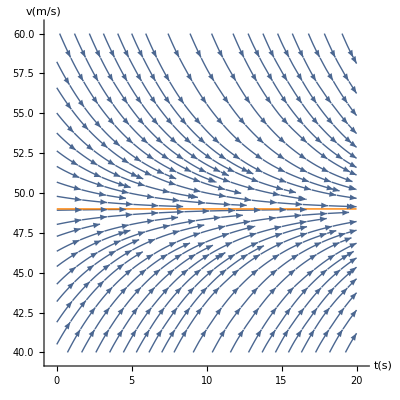

```mathematica
Show[StreamPlot[{1,9.8-v/5},{t,0,20},{v,40,60},Frame->False,Axes->True,AxesLabel->{"t(s)","v(m/s)"},AspectRatio->1],
Plot[49,{t,0,20},PlotStyle->{Orange,Thick}]
](*fig1.1.3*)
```

### Example 3: Field Mice and Owls

-Graphics-

If the mouse population, p(t) increases at a rate proportional to the current population, and 450 field mice per month are killed by owls, the populaiton growth can be expressed by the equation;

ⅆp/ⅆt==-450+0.5 p

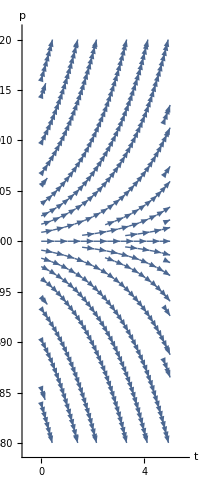

```mathematica
ⅆp/ⅆt==0.5p-450(*eq1.8*)
SCMAF[%,SCApplyFunc,{At[2],StreamPlot[{1,#},{t,0,5},{p,880,920},AxesLabel->{t,p},StreamPoints->Fine,Axes->True,Frame->False,AspectRatio->Full]&},Take->{2}]
```

```mathematica
ⅆp/ⅆt==0.5p-450(*eq1.8*)
SCMAF[%,RA,{At[1],ⅆp/ⅆt==0},
SCSolve,{All,p}]
```

ⅆp/ⅆt==-450+0.5 p

0==-450+0.5 p

p==900.

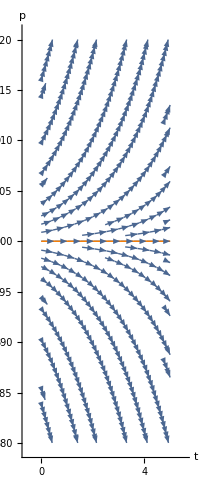

```mathematica
Show[StreamPlot[{1,-450+0.5 p},{t,0,5},{p,880,920},AxesLabel->{t,p},StreamPoints->Fine,Axes->True,Frame->False,AspectRatio->Full],
Plot[900,{t,0,5},PlotStyle->{Orange,Thick}]]
```

### Constructing Mathematical Models

Identify the independnet and dependent variables.

Choose the units of measurement for each variable.

Articularte the basic principle that underlies or governs the problem you are investigating.

Express the principle or law in step 3 in terms of the varibles you choose in step 1.

Make sure that all terms in your equation have the same physical units.

## 1.2 Solutions of Some Differential Equations

### Example 1: Field Mice and Owls (continued)

-Graphics-

```mathematica
ⅆp/ⅆt==0.5p-450(*eq2.4*)
SCMAF[%,RA,{At[2],0.5->1/2},Post->Together,
SCDivEq,{All,p-900},Post->SCDerivToFrac,
SCMultEq,{All,ⅆt},Post->SCDiffToInt,
SCEvalInt,{All,ReplConst->C},RA->{C[2]->0},
SCApplyFunc,{All,Exp},Level->{1},
SCSolve,{All,p},
SCEliminate,{At[2],ⅇ^(C/2)==c,C},RA->{C[1]==0}]
(*eq2.11*)
```

ⅆp/ⅆt==-450+0.5 p

p==900+ⅇ^(C/2+t/2)

p==900+c ⅇ^(t/2)

{900-60 ⅇ^(t/2),900-40 ⅇ^(t/2),900-20 ⅇ^(t/2),900,900+20 ⅇ^(t/2),900+40 ⅇ^(t/2),900+60 ⅇ^(t/2)}

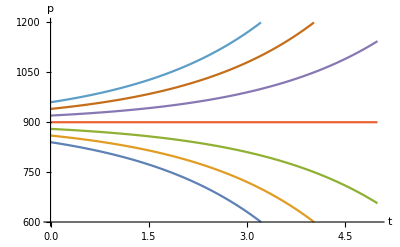

```mathematica
Table[Tooltip[900+c ⅇ^(t/2),"c="~~ToString[c]],{c,-60,60,20}]
Plot[Evaluate@%,{t,0,5},AxesLabel->{t,p},PlotRange->{600,1200}]
```

This geometrical representation of the general solution is an infinite family of curves called integral curves.

If an initial condition is gien,

```mathematica
p[t]==900+c ⅇ^(t/2)
SCMAF[%,RR,{All,{t==0,p[0]==850(*eq2.12*)}},
SCSolve,{All,c}]
```

p[t]==900+c ⅇ^(t/2)

850==900+c

c==-50

We obtain the desicred solution,

```mathematica
p==900+c ⅇ^(t/2)(*eq2.11*)
SCMAF[%,RA,{At[2],c==-50}]
(*eq2.13*)
```

p==900+c ⅇ^(t/2)

p==900-50 ⅇ^(t/2)

Or simplify,

```mathematica
{ⅆp/ⅆt==p/2-450,p[0]==850}
SCMAF[%,SCDSolve,{All,p,t},Post->Expand]
```

{ⅆp/ⅆt==-450+p/2,p[0]==850}

p==900-50 ⅇ^(t/2)

A diffeential equation together with an inital condition form an inital value problem.

Now consier the more general initial value problem,

```mathematica
ⅆy/ⅆt==a y- b
SCMAF[%,SCDivEq,{All,a},
SCDivEq,{All,y-b/a},
SCMultEq,{All,a},Post->SCDerivToFrac,
SCMultEq,{All,ⅆt},Post->SCDiffToInt,
SCEvalInt,{All,ReplConst->{C,0}},
SCApplyFunc,{All,Exp},Level->{1},
SCSolve,{All,y},Post->Expand,
SCEliminate,{At[2],c==ⅇ^C/a,C},RA->{C[1]==0}]
```

ⅆy/ⅆt==-b+a y

y==b/a+ⅇ^(C+a t)/a

y==b/a+c ⅇ^(a t)

where a≠0 and y≠b/a. y=b/a corresponds to the equilibrium solution. Finally, the initial condition (14) requires that

```mathematica
y[t]==b/a+c ⅇ^(a t)(*eq2.17*)
SCMAF[%,RR,{All,{t==0,y[0]==Subscript[y, 0]}},
SCSolve,{All,c}]
```

y[t]==b/a+c ⅇ^(a t)

y_0==b/a+c

c==(-b+a y_0)/a

so the solution of the initial value problem is

```mathematica
y==b/a+c ⅇ^(a t)(*eq2.17*)
SCMAF[%,RA,{At[2],c==(-b+a Subscript[y, 0])/a},
Expand,{(-b+a Subscript[y, 0])/a}]
(*eq2.18*)
```

y==b/a+c ⅇ^(a t)

y==b/a+(ⅇ^(a t) (-b+a y_0))/a

y==b/a+ⅇ^(a t) (-b/a+y_0)

For a≠0 the expression (17) contains all possible solutions of Eq. (3) and is called the general solution. If  a=0,

```mathematica
ⅆy/ⅆt==a y-b(*eq2.3*)
SCMAF[%,RA,{At[2],a==0},
SCDerivToFrac,{At[1]},
SCMultEq,{All,ⅆt},Post->SCDiffToInt,
SCEvalInt,{All,ReplConst->{0,-C}}]
```

ⅆy/ⅆt==-b+a y

∫1ⅆy==-∫bⅆt

y==C-b t

To relate the solution (18) to the model of field mouse population,

```mathematica
y==b/a+ⅇ^(a t) (-b/a+Subscript[y, 0])(*eq2.18*)
SCMAF[%,RA,{All,{y==p,a==r,b==k}}]
(*eq2.19*)
```

y==b/a+ⅇ^(a t) (-b/a+y_0)

p==k/r+ⅇ^(r t) (-k/r+p_0)

where p_0 is the initial population of field mice.

To relate the solution (18) to the model of a falling object,

```mathematica
y==b/a+ⅇ^(a t) (-b/a+Subscript[y, 0])(*eq2.18*)
SCMAF[%,RA,{All,{y==v,a==-γ/m,b==-g}}]
(*eq2.20*)
```

y==b/a+ⅇ^(a t) (-b/a+y_0)

v==(g m)/γ+ⅇ^(-(t γ)/m) (-(g m)/γ+v_0)

where v_0 is the inital velocity.

### Example 2: A Falling Object (continued)

-Graphics-

```mathematica
ⅆv/ⅆt==9.8-v/5(*eq2.21*)
SCMAF[%,RA,{At[2],9.8->98/10},
SCDSolve,{All,v[t],t}]
```

ⅆv/ⅆt==9.8-v/5

ⅆv/ⅆt==49/5-v/5

v[t]==49+ⅇ^(-t/5) C[1]

The object is dropped.

```mathematica
v[t]==49+ⅇ^(-t/5) C[1]
SCMAF[%,RR,{All,{t==0,v[0]==0(*eq2.22*)}},
SCSolve,{All,C[1]}]
```

v[t]==49+ⅇ^(-t/5) C[1]

0==49+C[1]

C[1]==-49

```mathematica
v[t]==49+ⅇ^(-t/5) C[1]
SCMAF[%,RA,{At[2],C[1]==-49},
SCFactor,{At[2],49}]
(*eq2.26*)
```

v[t]==49+ⅇ^(-t/5) C[1]

v[t]==49-49 ⅇ^(-t/5)

v[t]==49 (1-ⅇ^(-t/5))

The inetegral curves of general solutions are

{49-49 ⅇ^(-t/5),49-(49 ⅇ^(-t/5))/2,49,49+(49 ⅇ^(-t/5))/2,49+49 ⅇ^(-t/5)}

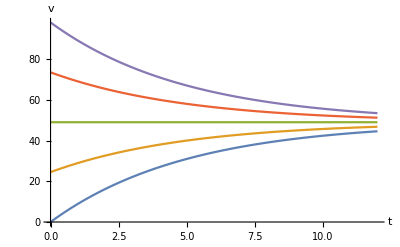

```mathematica
Table[Tooltip[49+ⅇ^(-t/5) C,"C="~~ToString[N@C]],{C,-49,49,49/2}]
Plot[Evaluate@%,{t,0,12},AxesLabel->{t,v}]
```

All solutios tend to approach the equilibrium solution v=49.

To find the velocity of the object when it hits the ground, we need to know the time at which impact occurs.

```mathematica
v[t]==49 (1-ⅇ^(-t/5))(*eq2.26*)
SCMAF[%,RA,{At[1],v[t]==ⅆx/ⅆt},Post->SCDerivToFrac,
SCMultEq,{All,ⅆt},Post->SCDiffToInt,
SCEvalInt,{All,ReplConst->{0,c/49}},Post->ExpandAll]
(*eq2.28*)
```

v[t]==49 (1-ⅇ^(-t/5))

∫1ⅆx==49 ∫(1-ⅇ^(-t/5))ⅆt

x==c+245 ⅇ^(-t/5)+49 t

The object starts to fall when t=0.

```mathematica
x==c+245 ⅇ^(-t/5)+49 t
SCMAF[%,RA,{All,{t==0,x==0}},
SCSolve,{All,c}]
```

x==c+245 ⅇ^(-t/5)+49 t

0==245+c

c==-245

```mathematica
x==c+245 ⅇ^(-t/5)+49 t(*eq2.28*)
SCMAF[%,RA,{At[2],c==-245}]
(*eq2.29*)
```

x==c+245 ⅇ^(-t/5)+49 t

x==-245+245 ⅇ^(-t/5)+49 t

Let T be th time at which the object hits the ground

```mathematica
x==-245+245 ⅇ^(-t/5)+49 t
SCMAF[%,RA,{All,{t==T,x==300}},
SCSolve,{All,T},Post->N]
```

x==-245+245 ⅇ^(-t/5)+49 t

300==-245+245 ⅇ^(-T/5)+49 T

{{T==10.5116},{T==-6.21803}}

At this time, the veloity v_T is

```mathematica
v[t]==49 (1-ⅇ^(-t/5))
SCMAF[%,RA,{All,t==T},
RA,{At[2],T==10.511583694277826}]
```

v[t]==49 (1-ⅇ^(-t/5))

v[T]==49 (1-ⅇ^(-T/5))

v[T]==43.0135